# Jeffrey-Kirwan residue formula in CoulombHiggs.m

As in [arXiv:1907.01354] we consider the Kronecker quiver of rank (2,3) with 3 arrows

```mathematica
SetDirectory[NotebookDirectory[]];
<<CoulombHiggs`
```

CoulombHiggs 5.0 - A package for evaluating quiver invariants

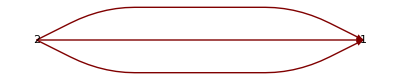

{(-1 | 0 | 1 | 0 | 0 | 0 | 3
0 | -1 | 1 | 0 | 0 | 0 | 3
-1 | 0 | 0 | 1 | 0 | 0 | 3
0 | -1 | 0 | 1 | 0 | 0 | 3
-1 | 0 | 0 | 0 | 1 | 0 | 3
0 | -1 | 0 | 0 | 1 | 0 | 3),{-624999937/1250000000,-1249999391/2500000000,2500002013/7500000000,62500063/187500000,7812509/23437500}}

```mathematica
Nvec={2,3};
Mat={{0,-3},{3,0}};
RMat=0Mat;
Cvec={-1,1}/Nvec;
QuiverPlot[Mat]

$QuiverNoVM=True;
$QuiverTrig=False;
$QuiverVerbose=False;

JKInitialize[Mat,RMat,Cvec,Nvec]
{JKChargeMatrix//MatrixForm, JKEta}
```

### First compute the index using Reineke’s formula

```mathematica
Higgs=Simplify[HiggsBranchFormula[Mat,Cvec,Nvec]];
{Series[Higgs,{y,1,0}],Higgs}
```

{13+O[y-1]^1,3+1/y^6+1/y^4+3/y^2+3 y^2+y^4+y^6}

### Next using the residue formula

```mathematica
JKIndex[JKChargeMatrix,Nvec,JKEta]
```

4 stable flags in total

From computing the Euler number, 4 stable flags appear to contribute

{-(7+27 y^2+55 y^4+69 y^6+55 y^8+27 y^10+7 y^12)/(2 y^6),-(-9-29 y^2-61 y^4-75 y^6-61 y^8-29 y^10-9 y^12)/(6 y^6),-(-9-29 y^2-61 y^4-75 y^6-61 y^8-29 y^10-9 y^12)/(6 y^6),-(-9-29 y^2-61 y^4-75 y^6-61 y^8-29 y^10-9 y^12)/(6 y^6)}

```mathematica
{Plus@@JKEuler,Expand[Plus@@JKChiGenus]}
```

{13,3+1/y^6+1/y^4+3/y^2+3 y^2+y^4+y^6}

```mathematica
JKListuDisplay={u1,u2,v1,v2,v3};
DisplayFlagList[JKRelevantStableFlags]
```

- List of (intersection point, stable flag, sign)

({0,0,0,0} | {-u1+v3,-u1+v2,-u1+v1,-u2+v3} | -1
{0,0,0,0} | {-u2+v3,-u1+v2,-u1+v1,-u1+v3} | -1
{0,0,0,0} | {-u1+v3,-u2+v2,-u1+v1,-u1+v2} | -1
{0,0,0,0} | {-u1+v3,-u1+v2,-u2+v1,-u1+v1} | -1)

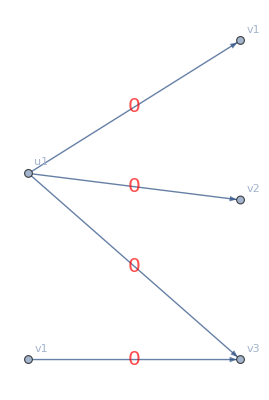
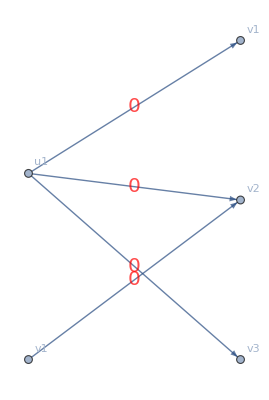
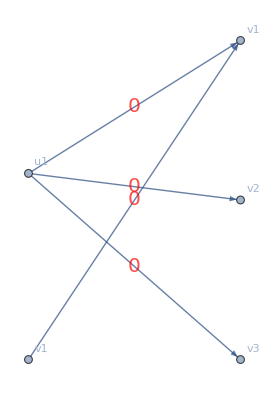
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
JKVertexLabels={1->u1,2->v1,3->v1,4->v2,5->v3};Table[DisplayFlagTree[JKRelevantStableFlags[[i]]],{i,Length[JKRelevantStableFlags]}]
```

### Same but applying the Cauchy-Bose formula on the first node

```mathematica
JKIndexSplit[JKChargeMatrix,Nvec,JKEta,{1}]
```

2 partitions with coefficient in table below:

({{2},{}} | 1
{{1,1},{}} | 1)

Partition{{2},{}}: 1 intersections, 4 stable flags in total

Partition{{1,1},{}}: 1 intersections, 4 stable flags in total

1 distinct intersections in total

Partition {{2},{}}

Partition {{1,1},{}}

From computing the Euler number, {4,4} stable flags appear to contribute:

Partition {{2},{}}

Partition {{1,1},{}}

{{-(1+8 y^2+28 y^4+56 y^6+70 y^8+56 y^10+28 y^12+8 y^14+y^16)/(2 y^8),-(-8-26 y^2-55 y^4-68 y^6-55 y^8-26 y^10-8 y^12)/(6 y^6),-(-8-26 y^2-55 y^4-68 y^6-55 y^8-26 y^10-8 y^12)/(6 y^6),-(-8-26 y^2-55 y^4-68 y^6-55 y^8-26 y^10-8 y^12)/(6 y^6)},{-(-1-y^2-y^4-y^6-y^8-y^10-y^12-y^14-y^16)/(2 y^8),-(-1-3 y^2-6 y^4-7 y^6-6 y^8-3 y^10-y^12)/(6 y^6),-(-1-3 y^2-6 y^4-7 y^6-6 y^8-3 y^10-y^12)/(6 y^6),-(-1-3 y^2-6 y^4-7 y^6-6 y^8-3 y^10-y^12)/(6 y^6)}}

```mathematica
{Plus@@JKEuler,Simplify[Plus@@JKChiGenus]}
```

{{-247/2,91/2,91/2,91/2},{-(7+27 y^2+55 y^4+69 y^6+55 y^8+27 y^10+7 y^12)/(2 y^6),(9+29 y^2+61 y^4+75 y^6+61 y^8+29 y^10+9 y^12)/(6 y^6),(9+29 y^2+61 y^4+75 y^6+61 y^8+29 y^10+9 y^12)/(6 y^6),(9+29 y^2+61 y^4+75 y^6+61 y^8+29 y^10+9 y^12)/(6 y^6)}}

```mathematica
Simplify[Normal[Series[Simplify[JKChiGenus],{y,1,0}]]]
```

{{-128,41,41,41},{9/2,9/2,9/2,9/2}}

```mathematica
Do[Print["Partition ",PermutationToPartition[JKListAllPerms[[i,1,1]]]];
DisplayFlagList[JKRelevantStableFlags[[i]]],{i,2}]
```

Partition {2}

- List of (intersection point, stable flag, sign)

({0,0,0,0} | {-u1+v3,-u1+v2,-u1+v1,-u2+v3} | -1
{0,0,0,0} | {-u2+v3,-u1+v2,-u1+v1,-u1+v3} | -1
{0,0,0,0} | {-u1+v3,-u2+v2,-u1+v1,-u1+v2} | -1
{0,0,0,0} | {-u1+v3,-u1+v2,-u2+v1,-u1+v1} | -1)

Partition {1,1}

- List of (intersection point, stable flag, sign)

({0,0,0,0} | {-u1+v3,-u1+v2,-u1+v1,-u2+v3} | -1
{0,0,0,0} | {-u2+v3,-u1+v2,-u1+v1,-u1+v3} | -1
{0,0,0,0} | {-u1+v3,-u2+v2,-u1+v1,-u1+v2} | -1
{0,0,0,0} | {-u1+v3,-u1+v2,-u2+v1,-u1+v1} | -1)

### Computing the equivariant chi-genus

```mathematica
RMat=2 FlavoredRMatrix[Mat]/.th[i_]:>Subscript[θ, i];
$QuiverNoVM=True;
$QuiverVerbose=False;
JKInitialize[Mat,RMat,Cvec,Nvec];
{JKChargeMatrix//MatrixForm, JKEta}
```

{(-1 | 0 | 1 | 0 | 0 | 2 θ_1 | 1
-1 | 0 | 1 | 0 | 0 | 2 θ_2 | 1
-1 | 0 | 1 | 0 | 0 | 2 θ_3 | 1
0 | -1 | 1 | 0 | 0 | 2 θ_1 | 1
0 | -1 | 1 | 0 | 0 | 2 θ_2 | 1
0 | -1 | 1 | 0 | 0 | 2 θ_3 | 1
-1 | 0 | 0 | 1 | 0 | 2 θ_1 | 1
-1 | 0 | 0 | 1 | 0 | 2 θ_2 | 1
-1 | 0 | 0 | 1 | 0 | 2 θ_3 | 1
0 | -1 | 0 | 1 | 0 | 2 θ_1 | 1
0 | -1 | 0 | 1 | 0 | 2 θ_2 | 1
0 | -1 | 0 | 1 | 0 | 2 θ_3 | 1
-1 | 0 | 0 | 0 | 1 | 2 θ_1 | 1
-1 | 0 | 0 | 0 | 1 | 2 θ_2 | 1
-1 | 0 | 0 | 0 | 1 | 2 θ_3 | 1
0 | -1 | 0 | 0 | 1 | 2 θ_1 | 1
0 | -1 | 0 | 0 | 1 | 2 θ_2 | 1
0 | -1 | 0 | 0 | 1 | 2 θ_3 | 1),{-312499997/625000000,-312499877/625000000,78125051/234375000,62500051/187500000,312500303/937500000}}

```mathematica
JKIndex[JKChargeMatrix,Nvec,JKEta];
```

348 stable flags in total

From computing the Euler number, 168 stable flags appear to contribute

```mathematica
Simplify[{Plus@@JKEuler,Plus@@JKChiGenus}]
```

{13,3+1/y^6+1/y^4+3/y^2+3 y^2+y^4+y^6}

```mathematica
(* Distinct contributions to equivariant Euler number *)
Tally[Simplify[JKEuler]]
```

{{0,180},{-((-1+θ_1-θ_2) (1+θ_1-θ_2) (-1+θ_1-θ_3) (1+θ_1-θ_3) (-1+θ_2-θ_3) (1+θ_2-θ_3))/(12 (θ_1-θ_2)^2 (θ_1-θ_3)^2 (θ_2-θ_3)^2),6},{((-1+θ_1-θ_2) (1+θ_1-θ_2) (-1+θ_1-θ_3) (1+θ_1-θ_3) (-1+θ_2-θ_3) (1+θ_2-θ_3))/(12 (θ_1-θ_2)^2 (θ_1-θ_3)^2 (θ_2-θ_3)^2),18},{-((1+θ_1-θ_3)^2 (1+2 θ_1-θ_2-θ_3) (1+θ_2-θ_3)^2 (-1+θ_1-2 θ_2+θ_3))/(12 (θ_1-θ_3)^2 (θ_2-θ_3)^2 (θ_1-2 θ_2+θ_3) (-2 θ_1+θ_2+θ_3)),12},{((-1+2 θ_1-2 θ_2) (-1+θ_1-θ_2) (-1+θ_1-θ_3) (1+θ_1-θ_3) (-1+θ_2-θ_3) (1+θ_2-θ_3))/(24 (θ_1-θ_2)^2 (θ_1-θ_3)^2 (θ_2-θ_3)^2),12},{((1+2 θ_1-2 θ_2) (1+θ_1-θ_2) (-1+θ_1-θ_3) (1+θ_1-θ_3) (-1+θ_2-θ_3) (1+θ_2-θ_3))/(24 (θ_1-θ_2)^2 (θ_1-θ_3)^2 (θ_2-θ_3)^2),12},{-((-1+2 θ_1-θ_2-θ_3) (1-θ_1+θ_3)^2 (1+θ_1-2 θ_2+θ_3) (1-θ_2+θ_3)^2)/(12 (θ_1-θ_3)^2 (θ_2-θ_3)^2 (θ_1-2 θ_2+θ_3) (-2 θ_1+θ_2+θ_3)),12},{((-1+θ_1-θ_2) (1+θ_1-θ_2) (1+2 θ_1-2 θ_3) (1+θ_1-θ_3) (-1+θ_2-θ_3) (1+θ_2-θ_3))/(24 (θ_1-θ_2)^2 (θ_1-θ_3)^2 (θ_2-θ_3)^2),12},{-((1-θ_1+θ_2)^2 (1+θ_1+θ_2-2 θ_3) (-1+2 θ_1-θ_2-θ_3) (1+θ_2-θ_3)^2)/(12 (θ_1-θ_2)^2 (θ_1+θ_2-2 θ_3) (θ_2-θ_3)^2 (-2 θ_1+θ_2+θ_3)),12},{-((1+θ_1-θ_2)^2 (-1+θ_1+θ_2-2 θ_3) (1+2 θ_1-θ_2-θ_3) (1-θ_2+θ_3)^2)/(12 (θ_1-θ_2)^2 (θ_1+θ_2-2 θ_3) (θ_2-θ_3)^2 (-2 θ_1+θ_2+θ_3)),12},{((-1+θ_1-θ_2) (1+θ_1-θ_2) (-1+2 θ_1-2 θ_3) (-1+θ_1-θ_3) (-1+θ_2-θ_3) (1+θ_2-θ_3))/(24 (θ_1-θ_2)^2 (θ_1-θ_3)^2 (θ_2-θ_3)^2),12},{((1+θ_1-θ_2)^2 (1+θ_1+θ_2-2 θ_3) (1+θ_1-θ_3)^2 (1+θ_1-2 θ_2+θ_3))/(12 (θ_1-θ_2)^2 (θ_1+θ_2-2 θ_3) (θ_1-θ_3)^2 (θ_1-2 θ_2+θ_3)),12},{((-1+θ_1-θ_2) (1+θ_1-θ_2) (1+2 θ_2-2 θ_3) (-1+θ_1-θ_3) (1+θ_1-θ_3) (1+θ_2-θ_3))/(24 (θ_1-θ_2)^2 (θ_1-θ_3)^2 (θ_2-θ_3)^2),12},{((-1+θ_1-θ_2) (1+θ_1-θ_2) (-1+2 θ_2-2 θ_3) (-1+θ_1-θ_3) (1+θ_1-θ_3) (-1+θ_2-θ_3))/(24 (θ_1-θ_2)^2 (θ_1-θ_3)^2 (θ_2-θ_3)^2),12},{((1-θ_1+θ_2)^2 (-1+θ_1+θ_2-2 θ_3) (1-θ_1+θ_3)^2 (-1+θ_1-2 θ_2+θ_3))/(12 (θ_1-θ_2)^2 (θ_1+θ_2-2 θ_3) (θ_1-θ_3)^2 (θ_1-2 θ_2+θ_3)),12}}

```mathematica
(* Distinct contributions to equivariant Chi genus number *)Tally[Simplify[(JKChiGenus/.Subscript[θ, i_]:>Log[Subscript[ν, i]]/2/Log[y])]]
```

{{-((y^2 ν_1-ν_2) (ν_1-y^2 ν_2) (y^2 ν_1-ν_3) (y^2 ν_2-ν_3) (ν_1-y^2 ν_3) (ν_2-y^2 ν_3))/(12 y^6 (ν_1-ν_2)^2 (ν_1-ν_3)^2 (ν_2-ν_3)^2),6},{((y^2 ν_1-ν_2) (ν_1-y^2 ν_2) (y^2 ν_1-ν_3) (y^2 ν_2-ν_3) (ν_1-y^2 ν_3) (ν_2-y^2 ν_3))/(12 y^6 (ν_1-ν_2)^2 (ν_1-ν_3)^2 (ν_2-ν_3)^2),18},{((-y^2 ν_1+ν_3)^2 (-y^2 ν_2+ν_3)^2 (-y^2 ν_2^2+ν_1 ν_3) (y^2 ν_1^2-ν_2 ν_3))/(12 y^6 (ν_1-ν_3)^2 (ν_2-ν_3)^2 (ν_2^2-ν_1 ν_3) (-ν_1^2+ν_2 ν_3)),12},{((ν_1-y^2 ν_2) (ν_1^2-y^2 ν_2^2) (y^2 ν_1-ν_3) (y^2 ν_2-ν_3) (ν_1-y^2 ν_3) (ν_2-y^2 ν_3))/(12 y^6 (ν_1-ν_2)^2 (ν_1+ν_2) (ν_1-ν_3)^2 (ν_2-ν_3)^2),12},{((y^2 ν_1-ν_2) (y^2 ν_1^2-ν_2^2) (y^2 ν_1-ν_3) (y^2 ν_2-ν_3) (ν_1-y^2 ν_3) (ν_2-y^2 ν_3))/(12 y^6 (ν_1-ν_2)^2 (ν_1+ν_2) (ν_1-ν_3)^2 (ν_2-ν_3)^2),12},{((ν_1-y^2 ν_3)^2 (ν_2-y^2 ν_3)^2 (-ν_2^2+y^2 ν_1 ν_3) (ν_1^2-y^2 ν_2 ν_3))/(12 y^6 (ν_1-ν_3)^2 (ν_2-ν_3)^2 (ν_2^2-ν_1 ν_3) (-ν_1^2+ν_2 ν_3)),12},{((y^2 ν_1-ν_2) (ν_1-y^2 ν_2) (y^2 ν_1-ν_3) (y^2 ν_2-ν_3) (ν_2-y^2 ν_3) (y^2 ν_1^2-ν_3^2))/(12 y^6 (ν_1-ν_2)^2 (ν_1-ν_3)^2 (ν_2-ν_3)^2 (ν_1+ν_3)),12},{((ν_1-y^2 ν_2)^2 (-y^2 ν_2+ν_3)^2 (ν_1^2-y^2 ν_2 ν_3) (y^2 ν_1 ν_2-ν_3^2))/(12 y^6 (ν_1-ν_2)^2 (ν_2-ν_3)^2 (ν_1^2-ν_2 ν_3) (ν_1 ν_2-ν_3^2)),12},{((-y^2 ν_1+ν_2)^2 (ν_2-y^2 ν_3)^2 (y^2 ν_1^2-ν_2 ν_3) (ν_1 ν_2-y^2 ν_3^2))/(12 y^6 (ν_1-ν_2)^2 (ν_2-ν_3)^2 (ν_1^2-ν_2 ν_3) (ν_1 ν_2-ν_3^2)),12},{((y^2 ν_1-ν_2) (ν_1-y^2 ν_2) (y^2 ν_2-ν_3) (ν_1-y^2 ν_3) (ν_2-y^2 ν_3) (ν_1^2-y^2 ν_3^2))/(12 y^6 (ν_1-ν_2)^2 (ν_1-ν_3)^2 (ν_2-ν_3)^2 (ν_1+ν_3)),12},{((-y^2 ν_1+ν_2)^2 (-y^2 ν_1+ν_3)^2 (-ν_2^2+y^2 ν_1 ν_3) (y^2 ν_1 ν_2-ν_3^2))/(12 y^6 (ν_1-ν_2)^2 (ν_1-ν_3)^2 (-ν_2^2+ν_1 ν_3) (ν_1 ν_2-ν_3^2)),12},{((y^2 ν_1-ν_2) (ν_1-y^2 ν_2) (y^2 ν_1-ν_3) (y^2 ν_2-ν_3) (ν_1-y^2 ν_3) (y^2 ν_2^2-ν_3^2))/(12 y^6 (ν_1-ν_2)^2 (ν_1-ν_3)^2 (ν_2-ν_3)^2 (ν_2+ν_3)),12},{((y^2 ν_1-ν_2) (ν_1-y^2 ν_2) (y^2 ν_1-ν_3) (ν_1-y^2 ν_3) (ν_2-y^2 ν_3) (ν_2^2-y^2 ν_3^2))/(12 y^6 (ν_1-ν_2)^2 (ν_1-ν_3)^2 (ν_2-ν_3)^2 (ν_2+ν_3)),12},{((ν_1-y^2 ν_2)^2 (ν_1-y^2 ν_3)^2 (-y^2 ν_2^2+ν_1 ν_3) (ν_1 ν_2-y^2 ν_3^2))/(12 y^6 (ν_1-ν_2)^2 (ν_1-ν_3)^2 (-ν_2^2+ν_1 ν_3) (ν_1 ν_2-ν_3^2)),12}}

```mathematica
(* in the limit y->1, each term contributes \pm 1/12 *)
Tally[Simplify[Simplify[(JKChiGenus/.Subscript[θ, i_]:>Log[Subscript[ν, i]]/2/Log[y])]/.y->1]]
```

{{-1/12,6},{1/12,162}}

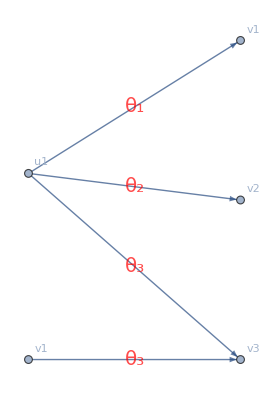
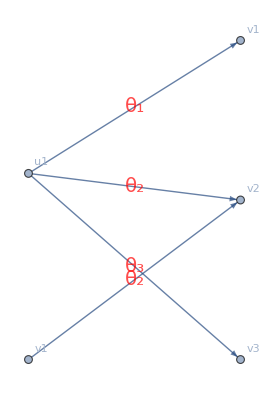
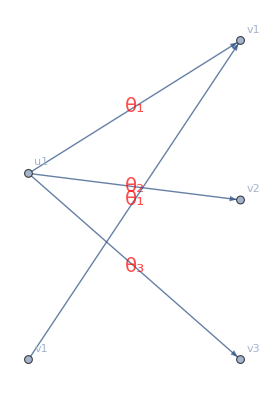
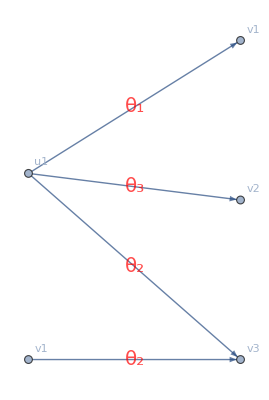
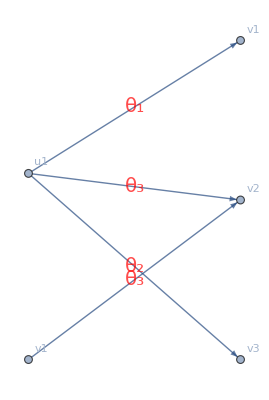
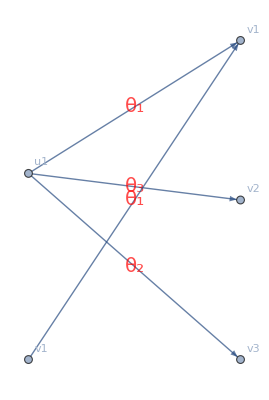
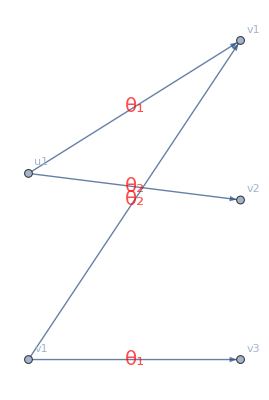
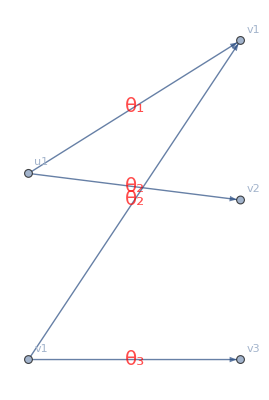
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
JKVertexLabels={1->u1,2->v1,3->v1,4->v2,5->v3};Table[DisplayFlagTree[JKRelevantStableFlags[[i]]],{i,Length[JKRelevantStableFlags]}]
```